# CCBH coupling and Power Law + Peak: Exclusion plots

Davi  C. Rodrigues (this code). May, 2023.

```mathematica
ResourceFunction["DarkMode"][]
```

CCBH = Cosmologically coupled Black Hole (arbitrary k value)
DEBH = Dark Energy coupled Black Hole (implies k = - 3w)
m1 = primary (larger) mass of the BBH or NSBH pair.

Naming conventions:
All defined variables/functions start with lower case letter.
“I" at the end of a function name: interpolated version. 
"Raw”: a function without options. It is useful to store results. The version with options is based on the raw version.

## Starting...

```mathematica
SetDirectory[NotebookDirectory[]];
<<"Directories.wl";

(*
  Calling Code files
  ****************** 
*)
getCode["Constants.wl"];
baseSimPoints = 3 10^5; (*The base number of points to be simmulated for each dimension, commonly 10^5-10^7, depends on the purpose.*)

getCode["ObsDataPreparationGWTC-3.wl"]; (*Not essential for this notebook*)
getCode["PowerLawPlusPeakDefinition.wl"];
getCode["Cosmology.wl"];
getCode["MassFactorCorrection.wl"];

Print["End of running wl files."];

(*
  GENERAL PURPOSE FUNCTIONS
  **************************
*)

findSigma::usage = "findSigma[probability] yields the number of σ's for a given probability.";
findSigma[prob_] := Block[{sigma}, 
  sigma /. FindRoot[NProbability[Abs[x] > sigma , x\[Distributed]NormalDistribution[]] == prob, {sigma, 2}]
];

Clear[outSigma];
outSigma[n_] := outSigma[n] = NProbability[Abs[x] > n, x\[Distributed]NormalDistribution[]];
```

Starting Constants.wl:

Starting ObsDataPreparationGWTC-3.wl:

Number of m1 black holes:   72

Starting PowerLawPlusPeakDefinition.wl:

Use plpp`pi[m, options] for the power-law-plus-peak PDF and plpp`𝒟[options] for the distribution. Use optionsPlpp to see the options.

Starting Cosmology.wl:

tableZformation loaded.

Starting MassFactorCorrection.wl:

Base number of simmulated points per dimension (baseSimPoints):   300000

"dataM1Merger"  4.8028

End of running wl files.

## Corner plots GBH and DEBH approaches (baseSimPoints = 3 x 10^5)

### Probability definition and testing

```mathematica
Clear[𝒟M1FormationEmpRaw,
  𝒟M1FormationEmp,
  probabilityMminApprox,
  probabilityMminDoubleApprox
];

position[list_, value_] := Position[list, value] /. {{x_}} -> x; (*useful for loading the data.*)

𝒟M1FormationEmpRaw[zObs_, tdmin_, tdmax_, k_, zMax_, w_] := 𝒟M1FormationEmpRaw[zObs, tdmin, tdmax, k, zMax, w] = 
 EmpiricalDistribution[
   dataM1FormationRaw[zObs, tdmin, tdmax, k, zMax, w]
 ];

𝒟M1FormationEmp[zObs_, opts:OptionsPattern[optionstkw]] := 𝒟M1FormationEmpRaw[
  zObs, 
  OptionValue @ tdmin, 
  OptionValue @ tdmax, 
  OptionValue @ k, 
  OptionValue @ zMax, 
  OptionValue @ w
];

probabilityMminApprox[mMin_, opts:OptionsPattern[optionstkw]] := SurvivalFunction[𝒟M1FormationEmp[0.4, opts], mMin]^72;
probabilityMminDoubleApprox[mMin_, opts:OptionsPattern[optionstkw]] := SurvivalFunction[𝒟M1FormationEmp[0.4, opts], mMin]^(2*72);
```

```mathematica
Echo[{probabilityMminApprox[2], findSigma[probabilityMminApprox[2]]}, "Probability and tension level in sigmas, current data: "];
Echo[{probabilityMminDoubleApprox[2], findSigma[probabilityMminDoubleApprox[2]]}, "Probability and tension level in sigmas, future data: "];
Echo[baseSimPoints, "baseSimPoints: "];
```

Probability and tension level in sigmas, current data:   {0.000234946,3.67813}

Probability and tension level in sigmas, future data:   {5.51996×10^-8,5.43369}

baseSimPoints:   300000

```mathematica
kValues = {0.5, 0.7, 0.9, 1.1, 1.3, 1.5, 1.7, 1.9, 2.1, 2.3, 2.5, 2.7, 2.9, 3.0}; 
wValues = Select[listw, -0.6 >= # >= -1&];
tdmaxValues = Range[3, 13, 1];
tdminValues = {0.005, 0.01, 0.02, 0.03, 0.04, 0.05}; 
zMaxValues = Range[2, 10, 1];
```

### Computing... And defining the probabilities

Organized in 3 groups: 
1. KT, KZ, KTmin
2. WT, WZ, WTmin
3. TZ, TTmin, ZTmin

IMPORTANT: The reading of the files need to be updated.

#### Computing KT, KZ, KTmin

```mathematica
isComputeTable𝒟M1KT = False; (*Takes about 4 minutes with baseSimPoints = 3 10^5*)

If[isComputeTable𝒟M1KT, 
  Echo["Computing..."];
  table𝒟M1KT = Table[
    𝒟M1FormationEmp[0.4, k-> k1, tdmax-> tdmax1], 
    {k1, kValues}, 
    {tdmax1, tdmaxValues}
  ]; // EchoTiming;
  dumpsave["tableDM1KT.mx", table𝒟M1KT],
  (*else*)
  getAux["tableDM1KT.mx"];
  Table[
    𝒟M1FormationEmp[0.4, k-> k1, tdmax-> tdmax1] = table𝒟M1KT[[position[kValues, k1], position[tdmaxValues, tdmax1]]], 
    {k1, kValues}, 
    {tdmax1, tdmaxValues}
  ];
  Echo["table𝒟M1KT loaded."];
];

tableProbKT = Table[
  {{k1, tdmax1}, probabilityMminApprox[2, k-> k1, tdmax -> tdmax1]}, 
  {k1, kValues}, 
  {tdmax1, tdmaxValues}
]; // EchoTiming

probabilityKT[k_, tdmax_] = Interpolation[Flatten[tableProbKT,1], InterpolationOrder -> 1][k, tdmax];
```

table𝒟M1KT loaded.

0.168272

It is necessary to implement the table used above to load the values in the codes below.

```mathematica
isComputeTable𝒟M1KZ = False; (*About 7 minutes with baseSimPoints = 3 10^5*)

If[isComputeTable𝒟M1KZ, 
  Echo["Computing..."];
  table𝒟M1KZ = Table[
    𝒟M1FormationEmp[0.4, k-> k1, zMax-> zMax1], 
    {k1, kValues}, 
    {zMax1, zMaxValues}
  ]; // EchoTiming;
  dumpsave["tableDM1KZ.mx", table𝒟M1KZ],
  (*else*)
  getAux["tableDM1KZ.mx"];
  Echo["table𝒟M1KZ loaded."];
];

tableProbKZ = Table[
  {{k1, zMax1}, probabilityMminApprox[2, k-> k1, zMax-> zMax1]}, 
  {k1, kValues}, 
  {zMax1, zMaxValues}
]; // EchoTiming

probabilityKZ[k_, zMax_] = Interpolation[Flatten[tableProbKZ,1], InterpolationOrder -> 1][k, zMax];
```

Computing...

453.263

0.215398

```mathematica
isComputeTable𝒟M1KTmin = False;  (*About 4 min*)

If[isComputeTable𝒟M1KTmin, 
  Echo["Computing..."];
  table𝒟M1KTmin = Table[
    𝒟M1FormationEmp[0.4, k-> k1, tdmin-> tdmin1], 
    {k1, kValues}, 
    {tdmin1, tdminValues}
  ]; // EchoTiming;
  dumpsave["tableDM1KTmin.mx", table𝒟M1KTmin],
  (*else*)
  getAux["tableDM1KTmin.mx"];
  Echo["table𝒟M1KTmin loaded."];
];

tableProbKTmin = Table[
  {{k1, tdmin1}, probabilityMminApprox[2, k-> k1, tdmin-> tdmin1]}, 
  {k1, kValues}, 
  {tdmin1, tdminValues}
]; // EchoTiming

probabilityKTmin[k_, tdmin_] = Interpolation[Flatten[tableProbKTmin,1], InterpolationOrder -> 1][k, tdmin];
```

Computing...

254.767

0.172304

#### Computing: wT, wZ, wTmin,

```mathematica
isComputeTable𝒟M1WT = False; (*Takes about 3 minutes with baseSimPoints = 2 10^5*)

If[isComputeTable𝒟M1WT, 
  Echo["Computing..."];
  table𝒟M1WT = Table[
    𝒟M1FormationEmp[0.4, k-> -3 w1, w -> w1, tdmax-> tdmax1], 
    {w1, wValues}, 
    {tdmax1, tdmaxValues}
  ]; // EchoTiming;
  dumpsave["tableDM1WT.mx", table𝒟M1WT],
  (*else*)
  getAux["tableDM1WT.mx"];
  Echo["table𝒟M1WT loaded."];
];

tableProbWT = Table[
  {{w1, tdmax1}, probabilityMminApprox[2, k-> -3 w1, w -> w1, tdmax-> tdmax1]}, 
  {w1, wValues}, 
  {tdmax1, tdmaxValues}
]; // EchoTiming

probabilityWT[w_, tdmax_] = Interpolation[Flatten[tableProbWT,1], InterpolationOrder -> 1][w, tdmax];
```

Computing...

222.541

0.094312

```mathematica
isComputeTable𝒟M1WZ = False; (*About 5 minutes *)

If[isComputeTable𝒟M1WZ, 
  Echo["Computing..."];
  table𝒟M1WZ = Table[
    𝒟M1FormationEmp[0.4, k-> - 3 w1, w -> w1, zMax-> zMax1], 
    {w1, wValues}, 
    {zMax1, zMaxValues}
  ]; // EchoTiming;
  dumpsave["tableDM1WZ.mx", table𝒟M1WZ],
  (*else*)
  getAux["tableDM1WZ.mx"];
  Echo["table𝒟M1WZ loaded."];
];

tableProbWZ = Table[
  {{w1, zMax1}, probabilityMminApprox[2, k-> - 3 w1, w -> w1, zMax-> zMax1]}, 
  {w1, wValues}, 
  {zMax1, zMaxValues}
]; // EchoTiming

probabilityWZ[w_, zMax_] = Interpolation[Flatten[tableProbWZ,1], InterpolationOrder -> 1][w, zMax];
```

Computing...

297.536

0.141921

```mathematica
isComputeTable𝒟M1WTmin = False; (*2-3 min*)

If[isComputeTable𝒟M1WTmin, 
  Echo["Computing..."];
  table𝒟M1WTmin = Table[
    𝒟M1FormationEmp[0.4, k-> - 3 w1, w-> w1, tdmin-> tdmin1], 
    {w1, wValues}, 
    {tdmin1, tdminValues}
  ]; // EchoTiming;
  dumpsave["tableDM1WTmin.mx", table𝒟M1WTmin],
  (*else*)
  getAux["tableDM1WTmin.mx"];
  Echo["table𝒟M1WTmin loaded."];
];

tableProbWTmin = Table[
  {{w1, tdmin1}, probabilityMminApprox[2, k-> - 3 w1, w-> w1, tdmin-> tdmin1]}, 
  {w1, wValues}, 
  {tdmin1, tdminValues}
]; // EchoTiming

probabilityWTmin[w_, tdmin_] = Interpolation[Flatten[tableProbWTmin,1], InterpolationOrder -> 1][w, tdmin];
```

Computing...

165.474

0.06963

#### Computing: TZ, TTmin, ZTmin

```mathematica
isComputeTable𝒟M1TZ = False; (*6 min*)

If[isComputeTable𝒟M1TZ, 
  Echo["Computing..."];
  table𝒟M1TZ = Table[
    𝒟M1FormationEmp[0.4, tdmax-> tdmax1, zMax-> zMax1], 
    {tdmax1, tdmaxValues}, 
    {zMax1, zMaxValues}
  ]; // EchoTiming;
  dumpsave["tableDM1TZ.mx", table𝒟M1TZ],
  (*else*)
  getAux["tableDM1TZ.mx"];
  Echo["table𝒟M1TZ loaded."];
];

tableProbTZ = Table[
  {{tdmax1, zMax1}, probabilityMminApprox[2, tdmax-> tdmax1, zMax-> zMax1]}, 
  {tdmax1, tdmaxValues}, 
  {zMax1, zMaxValues}
]; // EchoTiming

probabilityTZ[tdmax_, zMax_] = Interpolation[Flatten[tableProbTZ,1], InterpolationOrder -> 1][tdmax, zMax];
```

Computing...

376.059

0.13259

```mathematica
isComputeTable𝒟M1TTmin = False;  (*3-4 min*)

If[isComputeTable𝒟M1TTmin, 
  Echo["Computing..."];
  table𝒟M1TTmin = Table[
    𝒟M1FormationEmp[0.4, tdmax-> tdmax1, tdmin-> tdmin1], 
    {tdmax1, tdmaxValues}, 
    {tdmin1, tdminValues}
  ]; // EchoTiming;
  dumpsave["tableDM1TTmin.mx", table𝒟M1TTmin],
  (*else*)
  getAux["tableDM1TTmin.mx"];
  Echo["table𝒟M1TTmin loaded."];
];

tableProbTTmin = Table[
  {{tdmax1, tdmin1}, probabilityMminApprox[2, tdmax-> tdmax1, tdmin-> tdmin1]}, 
  {tdmax1, tdmaxValues}, 
  {tdmin1, tdminValues}
]; // EchoTiming

probabilityTTmin[tdmax_, tdmin_] = Interpolation[Flatten[tableProbTTmin,1], InterpolationOrder -> 1][tdmax, tdmin];
```

Computing...

220.596

0.07684

```mathematica
isComputeTable𝒟M1ZTmin = False; (*5 min*)

If[isComputeTable𝒟M1ZTmin, 
  Echo["Computing..."];
  table𝒟M1ZTmin = Table[
    𝒟M1FormationEmp[0.4, zMax-> zMax1, tdmin-> tdmin1], 
    {zMax1, zMaxValues}, 
    {tdmin1, tdminValues}
  ]; // EchoTiming;
  dumpsave["tableDM1ZTmin.mx", table𝒟M1ZTmin],
  (*else*)
  getAux["tableDM1ZTmin.mx"];
  Echo["table𝒟M1ZTmin loaded."];
];

tableProbZTmin = Table[
  {{zMax1, tdmin1}, probabilityMminApprox[2, zMax-> zMax1, tdmin-> tdmin1]}, 
  {zMax1, zMaxValues}, 
  {tdmin1, tdminValues}
]; // EchoTiming

probabilityZTmin[zMax_, tdmin_] = Interpolation[Flatten[tableProbZTmin,1], InterpolationOrder -> 1][zMax, tdmin];
```

Computing...

308.243

0.096924

### Plots

#### Plots of k vs probability

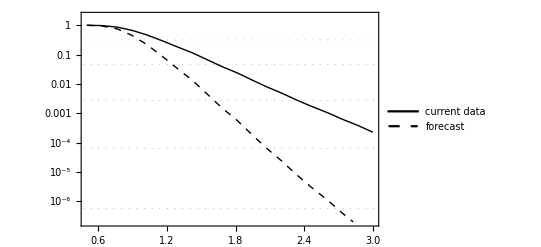

```mathematica
frameTicksSmall = Flatten[Table[{n 10^i, "", tickSmall}, {n,1,10}, {i, -10, 0, 1}],1];
frameTicksLarge = Table[{10^i, Superscript[10, i], tickLarge}, {i, -10, 0, 1}];
frameTicks = Join[frameTicksSmall, frameTicksLarge];
tickLarge = 0.015;
tickSmall = 0.006;


plotkProbability = Block[{},
  LogPlot[
    {
      probabilityKT[k, tdmax0],
      probabilityKT[k, tdmax0]^2
    },
    {k, 0.5, 3},
    PlotPoints -> 20,
    MaxRecursion->0,
    PlotStyle->{{Thick, Black}, {Thick, Black, Dashed}},
    Background->White,
    Frame -> True,
    Axes -> False,
    FrameStyle-> Directive[Black, FontSize -> 13],
    FrameTicksStyle-> Directive[Black, FontFamily-> "Times"],
    FrameTicks->{{frameTicks, {{outSigma[1], "1σ"}, {outSigma[2], "2σ"}, {outSigma[3], "3σ"}, {outSigma[4], "4σ"}, {outSigma[5], "5σ"}}}, {Automatic, Automatic}},
    GridLines->{None, {outSigma[1], outSigma[2], outSigma[3], outSigma[4], outSigma[5]}},
    GridLinesStyle->Directive[Gray, Dotted],
    PlotLegends-> Placed[
      {Style["current data", FontFamily->"Times", FontSize -> 14], Style["forecast", FontFamily->"Times", FontSize -> 14]}, 
      {0.3,0.3}
    ],
    PlotRange->{All, {2 10^-7, 2}}
  ]
]

(*exportOut["plotkProbability.pdf", plotkProbability]*)
```

```mathematica
FindRoot[(probabilityKT[k, tdmax0] //findSigma) == 2, {k, 1, 2}] // Quiet
```

{k→1.65111}

Now with Luca’s function

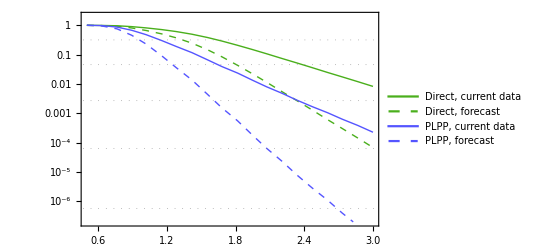

```mathematica
pointsLuca = {{0.2,0.9999999999979087},{0.30000000000000004,0.9999999999979087},{0.4,0.9999999999979087},{0.5,0.9979114858401865},{0.6000000000000001,0.9913076700861714},{0.7,0.9813534788396552},{0.8,0.9536970773327864},{0.9000000000000001,0.8958486726075061},{1.,0.8281748880287615},{1.1,0.7557367813610051},{1.2,0.6780132988000289},{1.3,0.5959458338676502},{1.4000000000000001,0.511524384871613},{1.5,0.42684725162977033},{1.6,0.34658463728522426},{1.7,0.276431967376146},{1.8,0.21638817172690022},{1.9000000000000001,0.1672760102091132},{2.,0.12851258171569166},{2.1,0.09820129368041103},{2.2,0.0748284009264067},{2.3000000000000003,0.0569030518896383},{2.4000000000000004,0.043213343356207384},{2.5000000000000004,0.03279174072861294},{2.6000000000000005,0.02487653404872536},{2.7,0.018874566684654762},{2.8000000000000003,0.014327865885673271},{2.9000000000000004,0.010885180158910268},{3.,0.008278492986420966}};
fullptabLuca[k_] = Interpolation[pointsLuca][k];

frameTicksSmall = Flatten[Table[{n 10^i, "", tickSmall}, {n,1,10}, {i, -10, 0, 1}],1];
frameTicksLarge = Table[{10^i, Superscript[10, i], tickLarge}, {i, -10, 0, 1}];
frameTicks = Join[frameTicksSmall, frameTicksLarge];
tickLarge = 0.015;
tickSmall = 0.006;


plotkProbabilityDirectPLPP = Block[{},
  LogPlot[
    {
      fullptab[k, 13],
      fullptab[k,13]^2,
      probabilityKT[k, tdmax0],
      probabilityKT[k, tdmax0]^2
    },
    {k, 0.5, 3},
    PlotPoints -> 20,
    MaxRecursion->0,
    PlotStyle->{{Thick, ColorData["AvocadoColors"][0.5]}, {Thick, ColorData["AvocadoColors"][0.5], Dashed}, {Thick, Lighter@Blue}, {Thick, Lighter@Blue, Dashed}},
    Background->White,
    Frame -> True,
    Axes -> False,
    FrameStyle-> Directive[Black, FontSize -> 13],
    FrameTicksStyle-> Directive[Black, FontFamily-> "Times"],
    FrameTicks->{{frameTicks, {{outSigma[1], "1σ"}, {outSigma[2], "2σ"}, {outSigma[3], "3σ"}, {outSigma[4], "4σ"}, {outSigma[5], "5σ"}}}, {Automatic, Automatic}},
    GridLines->{None, {outSigma[1], outSigma[2], outSigma[3], outSigma[4], outSigma[5]}},
    GridLinesStyle->Directive[Gray, Dotted],
    PlotLegends-> Placed[
      {Style["Direct, current data", FontFamily->"Times", FontSize -> 13], Style["Direct, forecast", FontFamily->"Times", FontSize -> 13], Style["PLPP, current data", FontFamily->"Times", FontSize -> 13], Style["PLPP, forecast", FontFamily->"Times", FontSize -> 13]}, 
      {0.27,0.25}
    ],
    PlotRange->{All, {2 10^-7, 2}}
  ]
]

exportOut["plotkProbabilityDirectPLPP.pdf", plotkProbabilityDirectPLPP]
```

#### The small mass population proportion

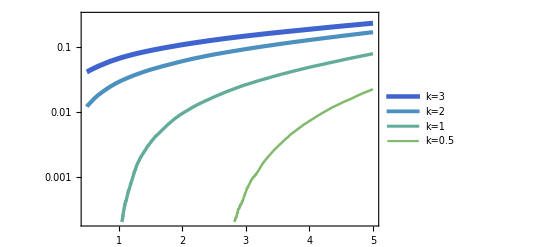

pathOut/plotSmallMassPopulation.pdf

```mathematica
frameTicksLarge = Table[{10^i, If[i<-2, ToString[10.^(i+2)]<>"%", ToString[10^(i+2)]<>"%"], tickLarge}, {i, -10, 0, 1}];
frameTicksLargeDumb = Table[{10^i, "", tickLarge}, {i, -10, 0, 1}];
frameTicksDumb = Join[frameTicksSmall, frameTicksLargeDumb];
frameTicks = Join[frameTicksSmall, frameTicksLarge];


plotSmallMassPopulation = LogPlot[
  {
    CDF[𝒟M1FormationEmp[0.4], m1],
    CDF[𝒟M1FormationEmp[0.4, k-> 2], m1], 
    CDF[𝒟M1FormationEmp[0.4, k-> 1], m1],
    CDF[𝒟M1FormationEmp[0.4, k-> 0.5], m1]
  }, 
  {m1, 0.5, 5},
  PlotStyle->{{Thickness[0.009], ColorData["Rainbow"][0.2]}, {ColorData["Rainbow"][0.3], Thickness[0.0075]}, {Thickness[0.006], ColorData["Rainbow"][0.4]}, {Thickness[0.0045], ColorData["Rainbow"][0.5]}},
  (*PlotStyle->{{Thickness[0.007], Lighter@Orange}, {ColorData[97, "ColorList"][[9]], Thickness[0.005]}, {Thickness[0.005], RGBColor[0.435, 0.518, 0.539]}, {Thickness[0.007], ColorData["AvocadoColors"][0.5]}}*)
  Background->White,
  Frame -> True,
  Axes -> False,
  FrameStyle-> Directive[Black, FontSize -> 13],
  FrameTicksStyle-> Directive[Black, FontFamily-> "Times"],
  FrameTicks->{{frameTicks, frameTicksDumb}, {Automatic, Automatic}},
  GridLines->{None, {10^-5, 10^-4, 10^-3, 10^-2, 10^-1}},
  GridLinesStyle->Directive[Gray, Dotted],
  PlotLegends-> Placed[
    {Style["k=3", FontFamily->"Times", FontSize -> 13], Style["k=2", FontFamily->"Times", FontSize -> 13], Style["k=1", FontFamily->"Times", FontSize -> 13], Style["k=0.5", FontFamily->"Times", FontSize -> 13]}, 
    {0.85,0.25}
  ],
  PlotRange->{{0.5, 5}, {2 10^-4, 0.3}}
]

exportOut["plotSmallMassPopulation.pdf", plotSmallMassPopulation]
```

```mathematica
ColorData["Rainbow"] /@ Range[0.2, 0.5, 0.1]
```

{RGBColor[0.2484884, 0.3863264, 0.813373],RGBColor[0.29795960000000005, 0.5657928, 0.7522386],RGBColor[0.38822480000000004, 0.674195, 0.6035436],RGBColor[0.513417, 0.72992, 0.440682]}

```mathematica
Range[0.2, 0.5, 0.1]
```

{0.2,0.3,0.4,0.5}

```mathematica
ColorData["Rainbow"][0.5]
```

RGBColor[0.513417, 0.72992, 0.440682]

#### Exclusion plots

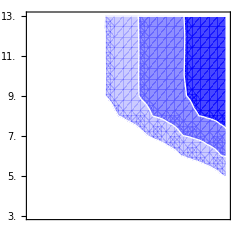

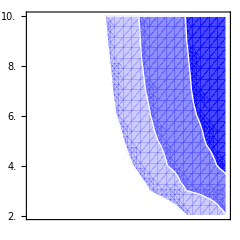

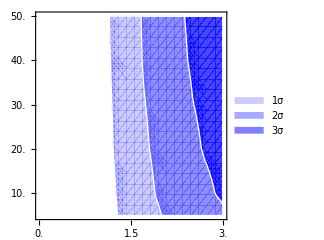

```mathematica
largeTick = 0.02;
smallTick = 0.01;

(*The ticks definitions:*)
frameTicksK = Table[If[IntegerPart[i]==i, {i/10., i/10., largeTick}, {i/10., "", smallTick}], {i, 0, 30, 2.5}];
frameTicksW = Table[If[IntegerPart[i]==i, {i/10., i/10., largeTick}, {i/10., "", smallTick}], {i, -10, -6.0, 0.5}];
frameTicksZ = Table[If[IntegerPart[i]==i, {i, i, largeTick}, {i, "", smallTick}], {i, 2., 10, 0.5}];
frameTicksTmin = Table[If[IntegerPart[i]==i, {i/100, i 10 (*Myr unit*), largeTick}, {i/100, "", smallTick}], {i, 0.0, 5, 0.5}];
frameTicksTmax = Table[If[IntegerPart[i]==i, {i, i, largeTick}, {i, "", smallTick}], {i, 3, 13, 0.5}];

(*Here the "dumb" ticks*)
frameTicksKD = frameTicksK /. {x_, y_, z_} -> {x, "", z}; 
frameTicksWD = frameTicksW /. {x_, y_, z_} -> {x, "", z}; 
frameTicksZD = frameTicksZ /.{x_, y_, z_} -> {x, "", z};
frameTicksTminD = frameTicksTmin /. {x_, y_, z_} -> {x, "", z};
frameTicksTmaxD = frameTicksTmax /.{x_, y_, z_} -> {x, "", z};

(*Sizes and spaces definitions*)
plotSize = 200;
spaceLeft = 30;
spaceBottom = 20;
spaceBetween = 10;

(*Setting general options for the RegionPlots*)
frameStyle = Directive[Black, FontSize -> 16, Thickness[0.005]];
frameTicksStyle = Directive[Black, FontFamily-> "Times"];
boundaryStyle = {1 -> Directive[White, Thin], 2 -> Directive[White, Thin], 3-> Directive[White, Thin]};
plotStyle = {Directive[Lighter@Blue, Opacity[0.3]], Directive[Lighter@Blue, Opacity[0.5]], Directive[Blue, Opacity[0.5]]};

SetOptions[RegionPlot, 
  PlotStyle -> plotStyle, 
  BoundaryStyle -> boundaryStyle, 
  FrameTicksStyle -> frameTicksStyle,
  FrameStyle -> frameStyle,
  PlotRangePadding -> None,
  Background -> White
];

(*The plots...*)

regionPlotKT2 = RegionPlot[
  {
    probabilityKT[k,tdmax] < outSigma[1],
    probabilityKT[k,tdmax] < outSigma[2],
    probabilityKT[k,tdmax] < outSigma[3]
  },
  {k, .5, 3}, {tdmax, First@tdmaxValues, tdmax0},
  FrameTicks -> {{frameTicksTmax, frameTicksTmaxD}, {frameTicksKD, frameTicksKD}},
  PlotRange -> {{0,3}, {First@tdmaxValues, tdmax0}},
  ImagePadding -> {{spaceLeft, spaceBetween}, {spaceBetween, spaceBetween}},
  ImageSize -> {plotSize +  spaceBetween + spaceLeft, plotSize + 2 spaceBetween}
]

regionPlotKZ2 = RegionPlot[
  {
    probabilityKZ[k,zMax] < outSigma[1],
    probabilityKZ[k,zMax] < outSigma[2],
    probabilityKZ[k,zMax] < outSigma[3]
  },
  {k, .5, 3}, {zMax, First@zMaxValues, zMax0},
  FrameTicks->{{frameTicksZ, frameTicksZD}, {frameTicksKD, frameTicksKD}},
  FrameTicksStyle-> Directive[Black, FontFamily-> "Times"],
  ImagePadding->{{spaceLeft, spaceBetween}, {spaceBetween, spaceBetween}},
  ImageSize->{plotSize + spaceBetween + spaceLeft, plotSize + 2 spaceBetween},
  PlotRange->{{0,3}, {First@zMaxValues, zMax0}}
]

regionPlotKTmin2 = RegionPlot[
  {
    probabilityKTmin[k,tdmin] < outSigma[1],
    probabilityKTmin[k,tdmin] < outSigma[2],
    probabilityKTmin[k,tdmin] < outSigma[3]
  },
  {k, .5, 3}, {tdmin, First@tdminValues, tdmin0},
  FrameTicks -> {{frameTicksTmin, frameTicksTminD},{frameTicksK, frameTicksKD}},
  ImagePadding->{{spaceLeft, spaceBetween}, {spaceBottom, spaceBetween}},
  ImageSize->{plotSize + spaceBetween + spaceLeft, plotSize + spaceBottom + spaceBetween},
  PlotLegends -> Placed[{
    Style["1σ", FontFamily->"Times", FontSize -> 18], 
    Style["2σ", FontFamily->"Times", FontSize -> 18], 
    Style["3σ", FontFamily->"Times", FontSize -> 18]}, 
    {0.15, 0.18}
  ],
  PlotRange->{{0,3}, {First@tdminValues, tdmin0}}
]
```

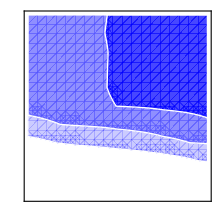

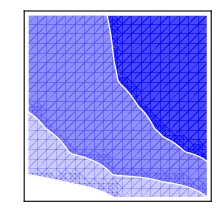

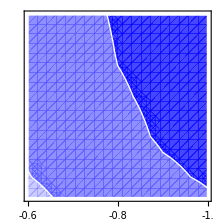

```mathematica
regionPlotWT2 = RegionPlot[
  {
    probabilityWT[w,tdmax] < outSigma[1],
    probabilityWT[w,tdmax] < outSigma[2],
    probabilityWT[w,tdmax] < outSigma[3]
  },
  {w,-1, -0.6}, {tdmax, First@tdmaxValues, tdmax0},
  FrameTicks -> {{frameTicksTmaxD, frameTicksTmaxD}, {frameTicksWD, frameTicksWD}},
  PlotRange -> {{-0.6,-1}, {First@tdmaxValues, tdmax0}},
  ImagePadding -> {{spaceBetween, spaceBetween}, {spaceBetween, spaceBetween}},
  ImageSize -> {plotSize + 2 spaceBetween, plotSize + 2 spaceBetween},
  ScalingFunctions -> {"Reverse", Identity}
]

regionPlotWZ2 = RegionPlot[
  {
    probabilityWZ[w,zMax] < outSigma[1],
    probabilityWZ[w,zMax] < outSigma[2],
    probabilityWZ[w,zMax] < outSigma[3]
  },
  {w, -0.6, -1}, {zMax, First@zMaxValues, zMax0},
  FrameTicks->{{frameTicksZD, frameTicksZD}, {frameTicksWD, frameTicksWD}},
  FrameTicksStyle-> Directive[Black, FontFamily-> "Times"],
  ImagePadding->{{spaceBetween, spaceBetween}, {spaceBetween, spaceBetween}},
  ImageSize->{plotSize + 2 spaceBetween, plotSize + 2 spaceBetween},
  PlotRange->{{-1, -0.6}, {First@zMaxValues, zMax0}},
  ScalingFunctions -> {"Reverse", Identity}
]

regionPlotWTmin2 = RegionPlot[
  {
    probabilityWTmin[w,tdmin] < outSigma[1],
    probabilityWTmin[w,tdmin] < outSigma[2],
    probabilityWTmin[w,tdmin] < outSigma[3]
  },
  {w, -0.6, -1}, {tdmin, First@tdminValues, tdmin0},
  FrameTicks -> {{frameTicksTminD, frameTicksTminD},{frameTicksW, frameTicksWD}},
  ImagePadding->{{spaceBetween,  spaceBetween}, {spaceBottom, spaceBetween}},
  ImageSize->{plotSize + 2 spaceBetween, plotSize + spaceBottom + spaceBetween},
  PlotRange->{{-1,-0.6}, {First@tdminValues, tdmin0}},
  ScalingFunctions -> {"Reverse", Identity}
]
```

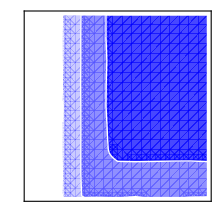

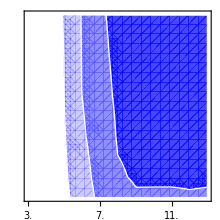

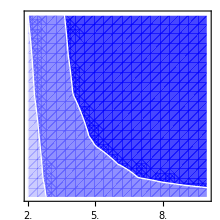

```mathematica
regionPlotTZ2 = RegionPlot[
  {
    probabilityTZ[tdmax,zMax] < outSigma[1],
    probabilityTZ[tdmax,zMax] < outSigma[2],
    probabilityTZ[tdmax,zMax] < outSigma[3]
  },
  {tdmax, First@tdmaxValues, tdmax0}, {zMax, First@zMaxValues, zMax0},
  FrameTicks->{{frameTicksZD, frameTicksZD},{frameTicksTmaxD, frameTicksTmaxD}},
  ImagePadding->{{spaceBetween, spaceBetween}, {spaceBetween, spaceBetween}},
  ImageSize->{plotSize + 2 spaceBetween, plotSize + 2 spaceBetween},
  PlotRange->{{First@tdmaxValues, tdmax0}, {First@zMaxValues, zMax0}}
]

regionPlotTTmin2 = RegionPlot[
  {
    probabilityTTmin[tdmax,tdmin] < outSigma[1],
    probabilityTTmin[tdmax,tdmin] < outSigma[2],
    probabilityTTmin[tdmax,tdmin] < outSigma[3]
  },
  {tdmax, First@tdmaxValues, tdmax0}, {tdmin, First@tdminValues, tdmin0},
  FrameTicks->{{frameTicksTminD, frameTicksTminD},{frameTicksTmax, frameTicksTmaxD}},
  ImagePadding->{{spaceBetween, spaceBetween}, {spaceBottom, spaceBetween}},
  ImageSize->{plotSize + 2 spaceBetween, plotSize + spaceBottom + spaceBetween},
  PlotRange->{{First@tdmaxValues, tdmax0}, {First@tdminValues, tdmin0}}
]

regionPlotZTmin2 = RegionPlot[
  {
    probabilityZTmin[zMax,tdmin] < outSigma[1],
    probabilityZTmin[zMax,tdmin] < outSigma[2],
    probabilityZTmin[zMax,tdmin] < outSigma[3]
  },
  {zMax, First@zMaxValues, zMax0}, {tdmin, First@tdminValues, tdmin0},
  FrameTicks->{{frameTicksTminD, frameTicksTminD},{frameTicksZ, frameTicksZD}},
  ImagePadding->{{spaceBetween, spaceBetween}, {spaceBottom, spaceBetween}},
  ImageSize->{plotSize + 2 spaceBetween, plotSize + spaceBottom + spaceBetween},
  PlotRange->{{First@zMaxValues, zMax0}, {First@tdminValues, tdmin0}}
]
```

```mathematica
cornerPlotCCBH = Grid[
  {
    {regionPlotKT2, regionPlotWT2},
    {regionPlotKZ2, regionPlotWZ2, regionPlotTZ2}, 
    {regionPlotKTmin2, regionPlotWTmin2, regionPlotTTmin2, regionPlotZTmin2}
  }, 
  Spacings -> {0,0}, 
  Background->White
]

exportOut["cornerPlotCCBH2.jpg", cornerPlotCCBH]
```

-Graphics- | -Graphics- |  | 
-Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-

pathOut/cornerPlotCCBH2.jpg

## Plots for the illustration with arrows

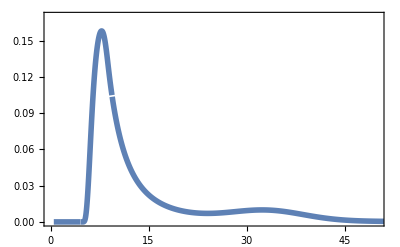

plotArrowsMerger.pdf

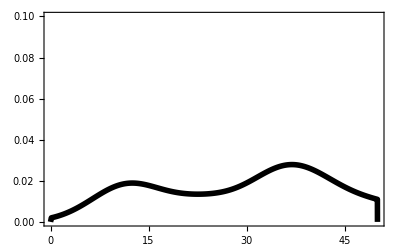

plotArrowsObs.pdf

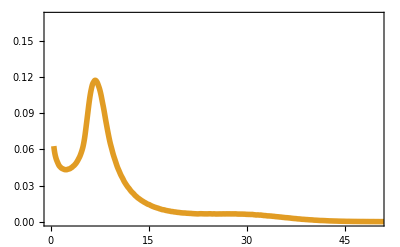

plotArrowsCCBH.pdf

```mathematica
plotArrowsMerger = Plot[
  {PDF[𝒟plp, x]}, 
  {x,0.5,100}, 
  PlotRange-> {{0,50}, {0,0.17}},
  Background->White,
  Frame -> True,
  Axes -> False,
  FrameStyle-> Directive[Black, FontSize -> 13],
  FrameTicksStyle-> Directive[Black, FontFamily-> "Times"],
  PlotPoints->2700,
  MaxRecursion->0,
  PlotStyle->{{Thickness[0.01], ColorData[97, "ColorList"][[1]]}}
]

Export["plotArrowsMerger.pdf", plotArrowsMerger]

plotArrowsObs = SmoothHistogram[
  mXzDataForPlotting[[All,2]] /. Around[x_,y_] ->  x, 
  5, 
  "PDF",  
  PlotRange->{{0,50}, {0,.10}}, 
  Background->White,
  Frame -> True,
  Axes -> False,
  FrameStyle-> Directive[Black, FontSize -> 13],
  FrameTicksStyle-> Directive[Black, FontFamily-> "Times"],
  PlotStyle->{{Thickness[0.01], Black}}
]

Export["plotArrowsObs.pdf", plotArrowsObs]

plotArrowsCCBH = Plot[
  {PDF[𝒟m1Formation, x]}, 
  {x,0.5,100}, 
  PlotRange-> {{0,50}, {0,0.17}},
  Background->White,
  Frame -> True,
  Axes -> False,
  FrameStyle-> Directive[Black, FontSize -> 13],
  FrameTicksStyle-> Directive[Black, FontFamily-> "Times"],
  PlotPoints->2700,
  MaxRecursion->0,
  PlotStyle->{{Thickness[0.01], ColorData[97, "ColorList"][[2]]}}
]

Export["plotArrowsCCBH.pdf", plotArrowsCCBH]
```

```mathematica
Plot[PDF[𝒟M1Formation[0.4], x], {x, 0,100}]
```

DataDistribution[<<SmoothKernel>>, {199307}]

## Formation mass distribution straight from observational data

```mathematica
Clear[dataM1ObsFormation];
mXzDataCentralValues = mXzDataForPlotting /. Around[x_, y_] -> x;

dataM1ObsFormation[k_, w_] := dataM1ObsFormation[k, w] =  #2 RandomVariate[𝒟InvMassFactor[#1, k, w], 10^5] &  @@@ mXzDataCentralValues;
```

```mathematica
dataM1ObsFormation[k0, w0] // EchoTiming; (*Check if it indeed has to be so long this computation*)
```

156.571

```mathematica
dataM1ObsFormationk0w0 = dataM1ObsFormation[k0, w0];
DumpSave["dataM1ObsFormationk0w0.mx", dataM1ObsFormationk0w0];
```

```mathematica
dataM1ObsFormation[k0, w0] // EchoTiming;

histFormationDistTest = Histogram[
  dataM1ObsFormation[k0, w0], 
  {0.4}, 
  "PDF", 
  PlotRange->{{0,100}, All},
  Background->White,
  Frame -> True,
  Axes -> False,
  FrameStyle-> Directive[Black, FontSize -> 13],
  FrameTicksStyle-> Directive[Black, FontFamily-> "Times"]
]
```

3.×10^-6

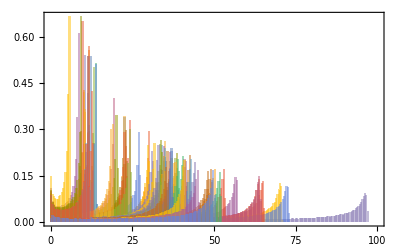

```mathematica
Clear[𝒟M1ObsFormation];
𝒟M1ObsFormation[bhNumber_, k_, w_] := 𝒟M1ObsFormation[bhNumber, k, w] = SmoothKernelDistribution[
  dataM1ObsFormation[k, w][[bhNumber]],
  0.1, 
  InterpolationPoints -> 10^5, 
  MaxExtraBandwidths -> {0,0}, 
  PerformanceGoal->"Quality"
]
```

```mathematica
𝒟M1ObsFormation[#, k0, w0] & /@ Range[72] // EchoTiming;
```

24.3162

```mathematica
PDF[𝒟M1ObsFormation[1, k0, w0], 20]
```

0.0142567

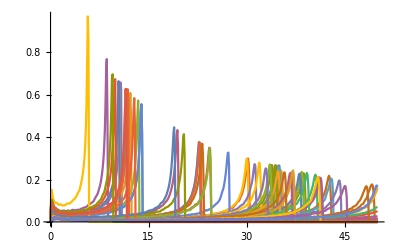

```mathematica
Block[
  {list = Table[{#, PDF[𝒟M1ObsFormation[i, k0, w0], #]} & /@ Range[0, 50, 0.1], {i,72}]},
  ListPlot[list, Joined->True, PlotRange->All]
]
```

```mathematica
probabilityGoodMass[bhNumber_, minimumMass_] := NProbability[m1 > minimumMass, m1 \[Distributed] 𝒟M1ObsFormation[bhNumber, k0, w0]];

totalProbabilityGoodMass[minimumMass_] := Product[probabilityGoodMass[bhNumber, minimumMass], {bhNumber, 1, 72}];
```

```mathematica
totalProbabilityGoodMass[2]
```

0.0101338

```mathematica
FindRoot[NProbability[Abs[x] > x0, x\[Distributed]NormalDistribution[]]==0.01 , {x0 , 2}]
```

{x0→2.57583}

## Probabilities for 2<m_th<5 (uses 10^6 Points) (OLD)

m_th is the threshold mass.

### Computing the relevant distributions

Before the applications, Loading or computing the relevant distributions,

```mathematica
listZobs = (mXzDataForPlotting1 /. Around[x_, y_] -> x)[[All,1]] // Sort;

isComputeTable𝒟M1FormationAllZobs = False; (*Change to True to compute and regenerate the mx file. About 15 min. with (baseSimPoints ~ 10^6)*)

If[isComputeTable𝒟M1FormationAllZobs, 
  Echo["Computing table𝒟M1FormationAllZobs..."];
  tableDM1FormationAllZobs = Table[
    {zObs, 𝒟M1Formation[zObs]}, 
    {zObs, DeleteDuplicates[listZobs]}
  ]; // EchoTiming;
  dumpsave["tableDM1FormationAllZobs.mx", tableDM1FormationAllZobs],
  (*else*)
  getAux["tableDM1FormationAllZobs.mx"];
  (𝒟M1Formation[#1] = #2) & @@@ tableDM1FormationAllZobs;
  Echo["tableDM1FormationAllZobs loaded."];
];
```

tableDM1FormationAllZobs loaded.

### Probabilities related with minimum mass from the above distributions

```mathematica
Clear[listProb, listProbRaw, probabilityMmin, probabilityMminApprox];
listProbRaw[mMin_, tdmin_, tdmax_, k_, zMax_, w_] := listProbRaw[mMin, tdmin, tdmax, k, zMax, w] = 
 NProbability[x>mMin, x \[Distributed] 𝒟M1FormationRaw[#, tdmin, tdmax, k, zMax, w]] & /@  listZobs;
listProb[mMin_, opts:OptionsPattern[optionstkw]] :=  listProbRaw[mMin, OptionValue @ tdmin, OptionValue @ tdmax, OptionValue @ k, OptionValue @ zMax, OptionValue @ w];

(*probabilityMmin[mMin_, opts:OptionsPattern[optionstkw]] :=  Times @@ listProb[mMin, opts];*)
probabilityMminApprox[mMin_, opts:OptionsPattern[optionstkw]] := NProbability[x>mMin, x \[Distributed] 𝒟M1Formation[0.4, opts]]^72;
probabilityMminDoubleApprox[mMin_, opts:OptionsPattern[optionstkw]] := NProbability[x>mMin, x \[Distributed] 𝒟M1Formation[0.4, opts]]^(2*72);

(*Echo[{probabilityMmin[2], findSigma[probabilityMmin[2]]}, "Probability that the model is correct and the sigma level of rejection: "]; (*taks about 10-15 minutes*)*)
Echo[{probabilityMminApprox[2], findSigma[probabilityMminApprox[2]]}, "Same as above, for the approximation case: "];
```

Same as above, for the approximation case:   {0.000659773,3.40577}

```mathematica
Clear[listProb, listProbRaw, probabilityMmin, probabilityMminApprox];(*It takes some minutes to compute the case without approximation*)
listProbRaw[mMin_, tdmin_, tdmax_, k_, zMax_, w_] := listProbRaw[mMin, tdmin, tdmax, k, zMax, w] = 
 NProbability[x>mMin, x \[Distributed] 𝒟M1FormationRaw[#, tdmin, tdmax, k, zMax, w]] & /@  listZobs;
listProb[mMin_, opts:OptionsPattern[optionstkw]] :=  listProbRaw[mMin, OptionValue @ tdmin, OptionValue @ tdmax, OptionValue @ k, OptionValue @ zMax, OptionValue @ w];

probabilityMmin[mMin_, opts:OptionsPattern[optionstkw]] :=  Times @@ listProb[mMin, opts];
probabilityMminApprox[mMin_, opts:OptionsPattern[optionstkw]] := NProbability[x>mMin, x \[Distributed] 𝒟M1Formation[0.4, opts]]^72;

Echo[{probabilityMmin[2], findSigma[probabilityMmin[2]]}, "Probability that the model is correct and the sigma level of rejection: "]; (*taks about 10-15 minutes*)
Echo[{probabilityMminApprox[2], findSigma[probabilityMminApprox[2]]}, "Same as above, for the approximation case: "];
```

Probability that the model is correct and the sigma level of rejection:   {0.000592407,3.43507}

Same as above, for the approximation case:   {0.000659773,3.40577}

Hence, with m_th = 2, the standard CCBH with k =3 is explided at more than 3 σ. Note that the approximation is quite good.

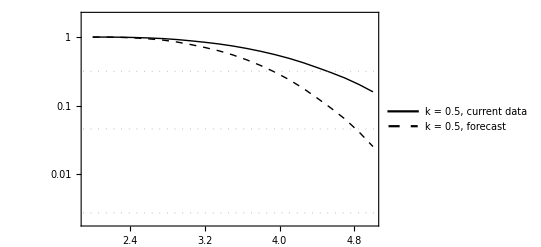

pathOut/plotProbabiliyNull005.pdf

```mathematica
frameTicksSmall = Flatten[Table[{n 10^i, "", tickSmall}, {n,1,10}, {i, -4, 0, 1}],1];
frameTicksLarge = Table[{10^i, Superscript[10, i], tickLarge}, {i, -4, 0, 1}];
frameticks = Join[frameTicksSmall, frameTicksLarge];
tickLarge = 0.015;
tickSmall = 0.006;


plotProbabiliyNull005 = Block[
  {
    list = {#, probabilityMminApprox[#, k-> 0.5] } & /@ Range[2,5,0.15],
    list2 = {#, probabilityMminDoubleApprox[#, k-> 0.5] } & /@ Range[2,5,0.15]
  },
  ListLogPlot[{list, list2}, 
    Joined->True,
    PlotStyle->{{Thick, Black}, {Thick, Black, Dashed}},
    Background->White,
    Frame -> True,
    Axes -> False,
    FrameStyle-> Directive[Black, FontSize -> 13],
    FrameTicksStyle-> Directive[Black, FontFamily-> "Times"],
    FrameTicks->{{frameticks, {{outSigma[1], "1σ"}, {outSigma[2], "2σ"}, {outSigma[3], "3σ"}}}, {Automatic, Automatic}},
    GridLines->{None, {outSigma[1], outSigma[2], outSigma[3]}},
    GridLinesStyle->Directive[Gray, Dotted],
    PlotLegends-> Placed[{Style["k = 0.5, current data", FontFamily->"Times", FontSize -> 14], Style["k = 0.5, forecast", FontFamily->"Times", FontSize -> 14]}, {0.3,0.2}],
    PlotRange->{All, {2 10^-3, 2}}
  ]
]

exportOut["plotProbabiliyNull005.pdf", plotProbabiliyNull005]
```

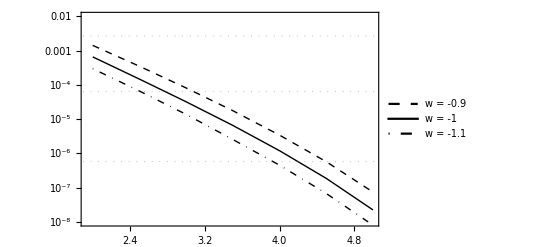

pathOut/plotProbabilityNullw.pdf

```mathematica
list1 = {#, probabilityMminApprox[#]} & /@ Range[2,5,0.5];
list2 = {#, probabilityMminApprox[#, k-> 3 0.9 , w-> -0.9]} & /@ Range[2,5,0.5];
list3 = {#, probabilityMminApprox[#, k-> 3 1.1 , w-> -1.1 ]} & /@ Range[2,5,0.5];

plotProbabilityNullw = Block[
  {numbers},
  numbers = Table[{10^-i, StringReplace["10^-a", "a" -> ToString[i]]}, {i, 1, 8, 2}];
  ListLogPlot[{list2, list1, list3}, 
    Joined->True,
    PlotStyle->{{Thick, Dashed, Black}, {Thick, Black}, {Thick, DotDashed, Black}},
    Background->White,
    Frame -> True,
    Axes -> False,
    FrameStyle-> Directive[Black, FontSize -> 13],
    FrameTicksStyle-> Directive[Black, FontFamily-> "Times"],
    FrameTicks->{{numbers, {{outSigma[1], "1σ"}, {outSigma[2], "2σ"}, {outSigma[3], "3σ"}, {outSigma[4], "4σ"}, {outSigma[5], "5σ"}}}, {Automatic, Automatic}},
    PlotRange->{All, {10^-8,  10^-2}},
    GridLines->{None, {outSigma[1], outSigma[2], outSigma[3], outSigma[4], outSigma[5]}},
    GridLinesStyle->Directive[Gray, Dotted],
    PlotLegends-> Placed[
      {
        Style["w = -0.9", FontFamily->"Times", FontSize -> 12], 
        Style["w = -1", FontFamily->"Times", FontSize -> 12], 
        Style["w = -1.1", FontFamily->"Times", FontSize -> 12]
      },
      {0.8,0.76}
    ]
  ]
]

exportOut["plotProbabilityNullw.pdf", plotProbabilityNullw]
```